```mathematica
L=10;DD=3/2;a=50;Subscript[a, ex]=a+2DD;S=1;
res =DSolve[{y''[x]-1/HoldForm[L]^2 y[x]==-HoldForm[S]/HoldForm[DD]DiracDelta[x], y[-Subscript[a, ex]]==0,y[Subscript[a, ex]]==0},y[x],x]//First//First;
```

```mathematica
Assuming[x>0,FullSimplify[y[x]/.res]]
Assuming[x<0,FullSimplify[y[x]/.res]]
```

(ⅇ^(-x/L) (ⅇ^(106/L)-ⅇ^((2 x)/L)) L S)/(2 (1+ⅇ^(106/L)) DD)

(ⅇ^(-x/L) (-1+ⅇ^((2 (53+x))/L)) L S)/(2 (1+ⅇ^(106/L)) DD)

```mathematica
Y[x_]=y[x]/.ReleaseHold[res];
```

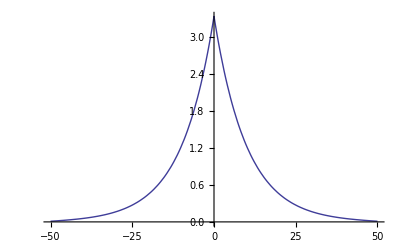

```mathematica
Plot[Y[x],{x,-a,a}]
```

```mathematica
N[{Y[0],Y[a]}]
```

{3.33317,0.0101334}